```mathematica
ClearAll[a1,a2,ca1,ca2,l1,l2]
```

```mathematica
a1[k_]:={-1 + ((2*k)/149),0};
a2[k_]:={-Cos[k π/149],0};
ca2[k_]:={-Cos[k π/149],-Sqrt[1-Cos[k π/149]^2]};
ca1[k_]:={-1 + ((2*k)/149),Sqrt[1-(-1+ ((2*k)/149))^2]};
l1[k_]:=Graphics[Line[{a1[k],ca1[k]}]];
l2[k_]:=Graphics[Line[{a2[k],ca2[k]}]];
```

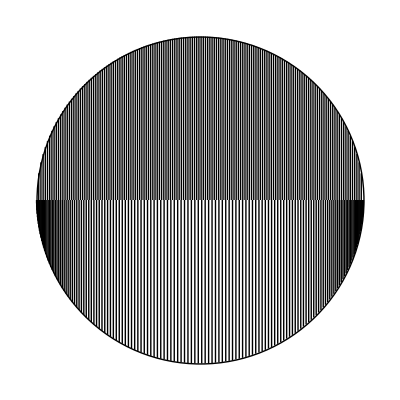

```mathematica
Show[{Table[l1[k],{k,0,149}],Table[l2[k],{k,0,149}],Graphics[Circle[]]}]
```

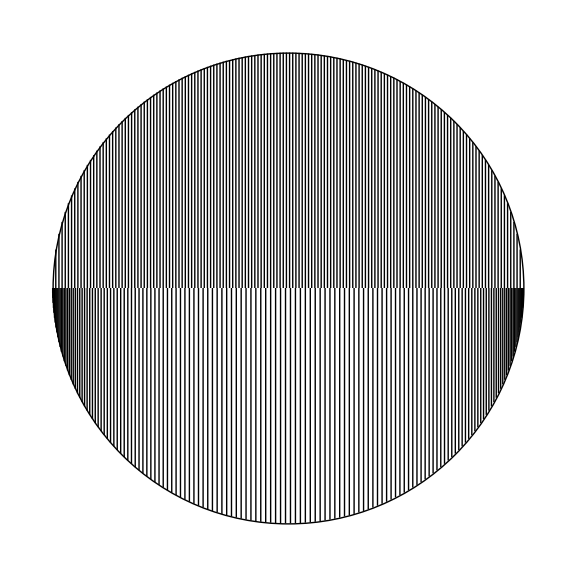

```mathematica
Show[%16,ImageSize->Large]
```

```mathematica
Export["/Users/shubhajitdey/Desktop/MS THESIS/TEX/figures/fig27.png",%17,"PNG"]
```

/Users/shubhajitdey/Desktop/MS THESIS/TEX/figures/fig27.png